```mathematica
ψ1[x_]:=(Q ⅇ^(-ⅈ Q L)+q ⅇ^(ⅈ q L)-qp ⅇ^(ⅈ k L))ⅇ^(ⅈ qm x)-(Q ⅇ^(ⅈ Q L)+q ⅇ^(-ⅈ q L)-qp ⅇ^(ⅈ k L) )ⅇ^(-ⅈ qm x)
ψ2[x_]:=-(Q ⅇ^(ⅈ Q L)-q ⅇ^(ⅈ q L)-qm ⅇ^(-ⅈ k L))ⅇ^(ⅈ k L) ⅇ^(ⅈ qp (x-L))+(Q ⅇ^(-ⅈ Q L)-q ⅇ^(-ⅈ q L)-qm ⅇ^(-ⅈ k L))ⅇ^(ⅈ k L)ⅇ^(-ⅈ qp (x-L))
```

```mathematica
(* Check Schrödinger equation *)
FullSimplify[{-D[ψ1[x],{x,2}]+(V/2)ψ1[x]==ϵ ψ1[x],-D[ψ2[x],{x,2}]-(V/2)ψ2[x]==ϵ ψ2[x]}//.{qp->√(ϵ+V/2),qm->√(ϵ-V/2),Q->(qp+qm)/2,q->(qp-qm)/2}]
(* Check smoothness at L/2 and periodicity *)
FullSimplify[{ψ1[L/2]==ψ2[L/2],ψ1'[L/2]==ψ2'[L/2],ψ2[L]==ψ1[0]Exp[ⅈ k L],ψ2'[L]==ψ1'[0]Exp[ⅈ k L]}//.{qp->√(ϵ+V/2),qm->√(ϵ-V/2),Q->(qp+qm)/2,q->(qp-qm)/2}]/.√(-V+2 ϵ) √(V+2 ϵ) (Cos[k L]-Cos[1/2 L √(-V/2+ϵ)] Cos[1/2 L √(V/2+ϵ)])+2 ϵ Sin[1/2 L √(-V/2+ϵ)] Sin[1/2 L √(V/2+ϵ)]->0
```

{True,True}

{True,True,True,True}

```mathematica
(* Eigenvalue equation *)
Simplify[√(-V+2 ϵ) √(V+2 ϵ) (Cos[k L]-Cos[1/2 L √(-V/2+ϵ)] Cos[1/2 L √(V/2+ϵ)])+2 ϵ Sin[1/2 L √(-V/2+ϵ)] Sin[1/2 L √(V/2+ϵ)]/.Cos[k L]->Cos[L/2 √(ϵ+V/2)]Cos[L/2 √(ϵ-V/2)]-ϵ Sin[L/2 √(ϵ+V/2)]/(√(ϵ+V/2))Sin[L/2 √(ϵ-V/2)]/(√(ϵ-V/2))]
```

0

```mathematica
(* Normalization *)
(* Assume ϵ-V/2 > 0 and ϵ+V/2 > 0. This seems to work in other cases too *)
FullSimplify[ComplexExpand[Re[ψ1[x]]^2]]
FullSimplify[ComplexExpand[Im[ψ1[x]]^2]]
I1=Simplify[Integrate[%%+%,{x,0,L/2}]/.{Q->(qp+qm)/2,q->(qp-qm)/2}];
FullSimplify[ComplexExpand[Re[ψ2[x]]^2]]
FullSimplify[ComplexExpand[Im[ψ2[x]]^2]]
I2=Simplify[Integrate[%%+%,{x,L/2,L}]/.{Q->(qp+qm)/2,q->(qp-qm)/2}];
Simplify[ExpandAll[ExpandAll[qp^2 qm^2(I1+I2)/.{Cos[k L]->Cos[L/2 qp]Cos[L/2 qm]-ϵ Sin[L/2 qp]/qp Sin[L/2 qm]/qm}]//.{qp^2->ϵ+V/2,qp^3->qp(ϵ+V/2),qp^4->(ϵ+V/2)^2,qm^2->ϵ-V/2,qm^3->qm(ϵ-V/2),qm^4->(ϵ-V/2)^2}]]
Simplify[1/(ϵ^2-(V/2)^2)%==((L V)/2(Cos[qp L]-Cos[qm L])+2 L ϵ (1-Cos[qp L]Cos[qm L])+L (1 +ϵ^2/(ϵ^2-(V/2)^2)) qp Sin[qp L]qm Sin[qm L]+(2 (V/2)^2)/(ϵ^2-(V/2)^2)((Cos[qp L]-1)qm Sin[qm L]+(Cos[qm L]-1)qp Sin[qp L]))]
```

4 qp^2 Sin[k L]^2 Sin[qm x]^2

4 (qp Cos[k L] Sin[qm x]+Q Sin[L Q-qm x]-q Sin[L q+qm x])^2

(q Cos[L (k+q-qp)+qp x]-Q Cos[L (k+Q-qp)+qp x]-q Cos[L q-L (k+qp)+qp x]+Q Cos[L Q-L (k+qp)+qp x])^2

(2 qm Sin[qp (L-x)]-q (Sin[L (k+q-qp)+qp x]+Sin[L q-L (k+qp)+qp x])+Q (Sin[L (k+Q-qp)+qp x]+Sin[L Q-L (k+qp)+qp x]))^2

1/8 (-V Cos[L qp] (L (V^2-4 ϵ^2)-4 qm V Sin[L qm])+Cos[L qm] (4 L ϵ (V^2-4 ϵ^2) Cos[L qp]+V (L V^2-4 L ϵ^2+4 qp V Sin[L qp]))-2 (2 (L ϵ (V^2-4 ϵ^2)+qp V^2 Sin[L qp])+qm Sin[L qm] (2 V^2+L qp (V^2-8 ϵ^2) Sin[L qp])))

True

```mathematica
Energy[V_?NumericQ,n_?NumericQ,K_?NumericQ]:=Module[{k=Abs[Abs[Mod[K/π-1,4]-2]-1]π},
Re[x/.FindRoot[Cos[k]-Cos[1/2 √(x+V/2)]Cos[1/2 √(x-V/2)]+x Sin[1/2 √(x+V/2)]/(√(x+V/2))Sin[1/2 √(x-V/2)]/(√(x-V/2)),{x,(If[n==1,-1,(n-1)^2]+n^2)/2 π^2,If[n==1,-1,(n-1)^2] π^2,n^2 π^2}]]]
```

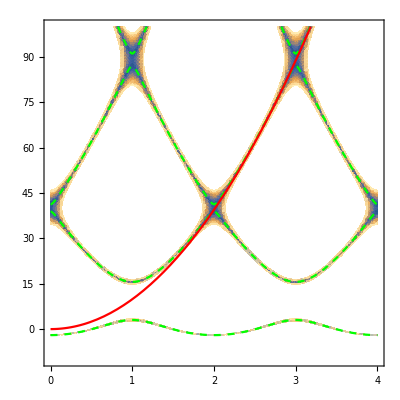

```mathematica
Show[DensityPlot[Abs[Cos[π k]-Cos[1/2 √(ϵ+V/2)]Cos[1/2 √(ϵ-V/2)]+ϵ Sin[1/2 √(ϵ+V/2)]/(√(ϵ+V/2))Sin[1/2 √(ϵ-V/2)]/(√(ϵ-V/2))/.V->20],{k,0,4},{ϵ,-10,100},PlotRange->{0,0.1},PlotPoints->100],Plot[{Energy[20,1,π k],Energy[20,2,π k],Energy[20,3,π k],Energy[20,4,π k]},{k,0,4},PlotRange->{-10,100},PlotStyle->{{Green,Dashed}}],Plot[π^2 k^2,{k,0,4},PlotRange->{-10,100},PlotStyle->Red]]
```

```mathematica
Showu[k_,n_]:=Module[{L,V,ϵ,qp,qm,Q,q,u,norm},
L=1;V=20;
ϵ=Energy[V,n,k];qp=√(ϵ+V/2); qm=√(ϵ-V/2); Q=(qp+qm)/2; q=(qp-qm)/2;
norm=L/2 V (Cos[L qp]-Cos[L qm])+2 L ϵ (1-Cos[L qm] Cos[L qp])+L qm qp  Sin[L qm] Sin[L qp]+(2qm (V/2)^2)/(ϵ^2-(V/2)^2)(Cos[L qp]-1)Sin[L qm]+(2qp (V/2)^2)/(ϵ^2-(V/2)^2)(Cos[L qm]-1)Sin[L qp]+(L qm qp ϵ^2)/(ϵ^2-(V/2)^2)Sin[L qm] Sin[L qp];
u[x_]:=Module[{X=Mod[x,L]},If[0≤X<L/2,(Q ⅇ^(-ⅈ Q L)+q ⅇ^(ⅈ q L)-qp ⅇ^(ⅈ k L))ⅇ^(ⅈ qm X)-(Q ⅇ^(ⅈ Q L)+q ⅇ^(-ⅈ q L)-qp ⅇ^(ⅈ k L) )ⅇ^(-ⅈ qm X),-(Q ⅇ^(ⅈ Q L)-q ⅇ^(ⅈ q L)-qm ⅇ^(-ⅈ k L))ⅇ^(ⅈ (k-qp) L) ⅇ^(ⅈ qp X)+(Q ⅇ^(-ⅈ Q L)-q ⅇ^(-ⅈ q L)-qm ⅇ^(-ⅈ k L))ⅇ^(ⅈ (k+qp)L)ⅇ^(-ⅈ qp X)]Exp[-ⅈ k X]/Sqrt[norm]];
If[Abs[NIntegrate[Abs[u[x]]^2,{x,0,L}]-1]<10^-12,Plot[{Re[u[x]],Im[u[x]]},{x,0,2L}]]
]
```

```mathematica
Manipulate[Showu[π k,n],{k,0,4},{n,1,4,1}]
```

```mathematica
FullSimplify[1/L Integrate[ψ1[x]Exp[-ⅈ K x],{x,0,L/2}]+1/L Integrate[ψ2[x]Exp[-ⅈ K x],{x,L/2,L}]/.k->K-(2π)/L m,{m∈Integers}]
```

1/L ⅈ ((ⅇ^(ⅈ L q) (-1+ⅇ^(1/2 ⅈ L (-K+qm))) q)/(K-qm)+(ⅇ^(-ⅈ L Q) (-1+ⅇ^(1/2 ⅈ L (-K+qm))) Q)/(K-qm)+(ⅇ^(-1/2 ⅈ L (K+2 q+qm)) (-1+ⅇ^(1/2 ⅈ L (K+qm))) q)/(K+qm)+(ⅇ^(ⅈ L Q) (1-ⅇ^(-1/2 ⅈ L (K+qm))) Q)/(K+qm)+(ⅇ^(1/2 ⅈ L (K+2 q-qp)) (-1+ⅇ^(1/2 ⅈ L (-K+qp))) q)/(K-qp)-(ⅇ^(1/2 ⅈ L (K+2 Q-qp)) (-1+ⅇ^(1/2 ⅈ L (-K+qp))) Q)/(K-qp)-(ⅇ^(-ⅈ K L) (-1+ⅇ^(1/2 ⅈ L (K-qp))) qm)/(K-qp)-(ⅇ^(ⅈ K L) (-1+ⅇ^(1/2 ⅈ L (-K+qm))) qp)/(K-qm)-(ⅇ^(1/2 ⅈ L (K-qm)) (-1+ⅇ^(1/2 ⅈ L (K+qm))) qp)/(K+qm)+(ⅇ^(-ⅈ L q) (-1+ⅇ^(1/2 ⅈ L (K+qp))) q)/(K+qp)-(ⅇ^(-ⅈ L Q) (-1+ⅇ^(1/2 ⅈ L (K+qp))) Q)/(K+qp)+(ⅇ^(-ⅈ K L) (-1+ⅇ^(1/2 ⅈ L (K+qp))) qm)/(K+qp))

```mathematica
A[V_?NumericQ,n_?NumericQ,K_?NumericQ]:=Module[{k,ϵ,qp,qm,Q,q,norm},k=Abs[Abs[Mod[K/π-1,4]-2]-1]π;
ϵ=Energy[V,n,k];qp=√(ϵ+V/2); qm=√(ϵ-V/2); Q=(qp+qm)/2; q=(qp-qm)/2;
norm=Abs[1/2 V (Cos[qp]-Cos[qm])+2 ϵ (1-Cos[qm] Cos[qp])+qm qp  Sin[qm] Sin[qp]+(2qm (V/2)^2)/(ϵ^2-(V/2)^2)(Cos[qp]-1)Sin[qm]+(2qp (V/2)^2)/(ϵ^2-(V/2)^2)(Cos[qm]-1)Sin[qp]+(qm qp ϵ^2)/(ϵ^2-(V/2)^2)Sin[qm] Sin[qp]];
Abs[ⅈ ((ⅇ^(ⅈ q) (-1+ⅇ^(1/2 ⅈ (-K+qm))) q)/(K-qm)+(ⅇ^(-ⅈ Q) (-1+ⅇ^(1/2 ⅈ (-K+qm))) Q)/(K-qm)+(ⅇ^(-1/2 ⅈ (K+2 q+qm)) (-1+ⅇ^(1/2 ⅈ (K+qm))) q)/(K+qm)+(ⅇ^(ⅈ Q) (1-ⅇ^(-1/2 ⅈ (K+qm))) Q)/(K+qm)+(ⅇ^(1/2 ⅈ (K+2 q-qp)) (-1+ⅇ^(1/2 ⅈ (-K+qp))) q)/(K-qp)-(ⅇ^(1/2 ⅈ (K+2 Q-qp)) (-1+ⅇ^(1/2 ⅈ (-K+qp))) Q)/(K-qp)-(ⅇ^(-ⅈ K) (-1+ⅇ^(1/2 ⅈ (K-qp))) qm)/(K-qp)-(ⅇ^(ⅈ K) (-1+ⅇ^(1/2 ⅈ (-K+qm))) qp)/(K-qm)-(ⅇ^(1/2 ⅈ (K-qm)) (-1+ⅇ^(1/2 ⅈ (K+qm))) qp)/(K+qm)+(ⅇ^(-ⅈ q) (-1+ⅇ^(1/2 ⅈ (K+qp))) q)/(K+qp)-(ⅇ^(-ⅈ Q) (-1+ⅇ^(1/2 ⅈ (K+qp))) Q)/(K+qp)+(ⅇ^(-ⅈ K) (-1+ⅇ^(1/2 ⅈ (K+qp))) qm)/(K+qp))]^2/norm]
```

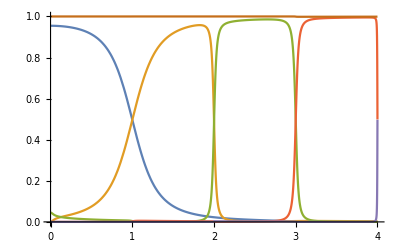

```mathematica
Plot[{A[20,1,π K],A[20,2,π K],A[20,3,π K],A[20,4,π K],A[20,5,π K],A[20,1,π K]+A[20,2,π K]+A[20,3,π K]+A[20,4,π K]+A[20,5,π K]},{K,0,4},PlotRange->All]
```

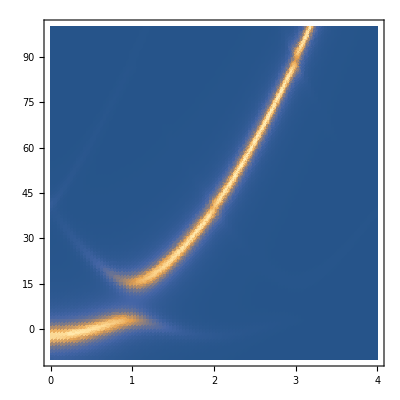

```mathematica
Γ=2;
DensityPlot[A[20,1,π K](Γ/π)/((ϵ-Energy[20,1,π K])^2+Γ^2)+A[20,2,π K](Γ/π)/((ϵ-Energy[20,2,π K])^2+Γ^2)+A[20,3,π K](Γ/π)/((ϵ-Energy[20,3,π K])^2+Γ^2)+A[20,4,π K](Γ/π)/((ϵ-Energy[20,4,π K])^2+Γ^2),{K,0,4},{ϵ,-10,100},PlotRange->All,PlotPoints->100]
```